```mathematica
heqn=Laplacian[u[x,y],{x,y}]==0
ic={u[x,0]==40*Sin[(Pi*x)/2],u[x,1]==40,u[0,y]==40*y^2,u[1,y]==40}

sol=DSolveValue[{heqn,ic},u[x,y],{x,y}];
asol=sol/.{∞-> 2}//Activate
Plot3D[Evaluate[asol],{x,0,1},{y,0,1},Exclusions->None,PlotRange->All]
```

u^(0,2)[x,y]+u^(2,0)[x,y]==0

{u[x,0]==40 Sin[(π x)/2],u[x,1]==40,u[0,y]==40 y^2,u[1,y]==40}

-(80 (4-π^2) Csch[π] Sin[π y] Sinh[π (1-x)])/π^3-(40 Csch[2 π] Sin[2 π y] Sinh[2 π (1-x)])/π+(160 Csch[π] Sin[π y] Sinh[π x])/π+(320 Csch[π] Sin[π x] Sinh[π (1-y)])/(3 π)-(128 Csch[2 π] Sin[2 π x] Sinh[2 π (1-y)])/(3 π)+(160 Csch[π] Sin[π x] Sinh[π y])/π

-Graphics3D-

```mathematica
Sol=ReadList["C:\\Users\\Коптутер\\source\\repos\\Лаба 5\\Лаба 5\\Solution.txt",{Number,Number,Number}];
ListPlot3D[Sol]
```

-Graphics3D-

```mathematica
usol=NDSolveValue[{Laplacian[u[x,y],{x,y}]==0,u[x,0]==40*Sin[(Pi*x)/2],u[x,1]==40,u[0,y]==40*y^2,u[1,y]==40},u,{y,0,1},{x,0,1}];

Plot3D[usol[y,x],{x,0,1},{y,0,1}]
```

-Graphics3D-

{-4.60517,-3.91202,-3.21888,-2.52573}

{-5.23713,-4.45682,-3.56943,-2.3279}

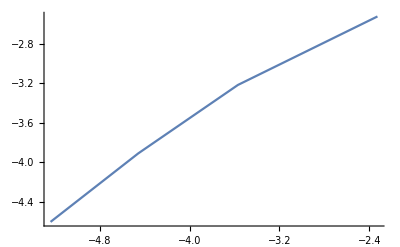

```mathematica
SolPX=ReadList["C:\\Users\\Коптутер\\source\\repos\\Лаба2\\Лаба2\\SolutionPres 2X.txt",{Number}];

X1=Table[0,250];
X2=Table[0,125];
X3=Table[0,62];
X4=Table[0,31];
For[i=1,i≤250,i++,
X1[[i]]=SolPX[[i]]
]
For[i=251,i≤375,i++,
X2[[i-250]]=SolPX[[i]]
]
For[i=376,i≤437,i++,
X3[[i-375]]=SolPX[[i]]
]
For[i=438,i≤468,i++,
X4[[i-437]]=SolPX[[i]]
]


n={Log[0.01],
Log[0.02],
Log[0.04],
Log[0.08]}
EPS={Log [Max[X1]],
Log [Max[X2]],
Log [Max[X3]],
Log [Max[X4]]}

ListLinePlot[{{Log [Max[X4]],Log[0.08]},{Log [Max[X3]],Log[0.04]},{Log [Max[X2]],Log[0.02]},{Log [Max[X1]],Log[0.01]}}]
```